```mathematica
(* This allows us to explicitly state our assumptions about variables making ComplexExpand fully simplify on variables we assume are real *)
$Assumptions={};
Assume[assumptions_]:=$Assumptions=DeleteDuplicates@Flatten@Append[$Assumptions,assumptions]
Assume[{p,q,u,v,x,y,a,b,c}∈Reals];
```

## Notation Conventions

```mathematica
(*  2.1 The Variable X is a member of the Lie algebra of su(3), a skew-hermitian 3×3 complex matrix with trace zero *) 
X=({{I a, r, s}, {-r*, I b, t}, {-s*, -t*, I c}});
(*  Variables {p,q,u,v,x,y,a,b,c} ∈ Reals  *)
r=p + I q;
s=u + I v;
t=x + I y;

(* r* is complex conjugate of r, etc.  *)
X=X//ComplexExpand;
```

```mathematica
(* Differences used in the computation of of β̃ function, see eq.9 *)
μ[1,2]=μ[2]-μ[1];
μ[1,3]=μ[3]-μ[1];
μ[2,3]=μ[3]-μ[2];
```

## Symplectic Form and Hamiltonian Vector Field

```mathematica
(* §3.1 Euclidean Inner Product of tangent vectors to su(3)
     thought of as matrices in su(3) *)
IP[A_,B_]:=-Tr[A.B];

(* §3.1 Commutator, denoted [A,B] *)
Comm[A_,B_]:=A.B-B.A
```

```mathematica
(* §3.2: e1 and e2 are two arbitrary elements in su(3) 
chosen to create a basis for our variety ℳ *)
e1 = SparseArray[{{1,2}->r,{2,1}->-r*},{3,3}]//Simplify;
e2 = SparseArray[{{1,3}->s,{3,1}->-s*},{3,3}]//Simplify;

(* We wish to find β(e) satisfying [X,e] = [Iμ,β(e)], e ∈ su(3) *)

(* §3.1 eq.19: To achieve this we define β̃  *)
β̃[e_]:=-{{0, -I e[[1,2]]/μ[1,2], -I e[[1,3]]/μ[1,3]},{I e[[2,1]]/μ[1,2],0, -I e[[2,3]]/μ[2,3]},{I e[[3,1]]/μ[1,3], I e[[3,2]]/μ[2,3],0}}//ComplexExpand

(* §3.1 eq.20: β̃ allows us to define the desired vector field β(e) *)
β[e_]:=β̃[Comm[X,e]]
```

```mathematica
α[e_]:=-e-β[e]
(* §3.1 eq.20 *)
V[e_]:=Comm[X,α[e]]

V1=V[e1]//Simplify;
V2=V[e2]//Simplify;
```

## Equations Characterizing the Triple Reduced Product

```mathematica
(* μ is Real, Skew, and Symmetric *)
(* LAM  and NU are constant matrices in the original problem *)
(* Later we will specify λs and νs to compute specific solutions*)

MU:=I DiagonalMatrix[{μ[1], μ[2], μ[3]}]; (* Iμ in paper *)
LAM=I DiagonalMatrix[{λ1,λ2,λ3}]; (* Iλ in paper *)
NU = I DiagonalMatrix[{ν1,ν2,ν3}]; (* Iν in paper *)
```

```mathematica
(* §2.2: τ2 is the second elementary symetric polynomial Subscript[τ, 2](X) *)
τ2[X_] := Coefficient[Det[X- z IdentityMatrix[3]], z]

(* Quality of life function simplifying difference between common τ2 evaluations*)
τdiff=τ2[-X-MU]-τ2[-X];
(* Quality of life function simplifying difference between common Det evaluations*)
detsum=Det[-X - MU] + Det[X];
```

```mathematica
(* Equations characterizing the triple reduced product *)
eqn1:=I(detsum-Det[NU]-Det[LAM])//ComplexExpand;
eqn2:=I(Det[X]-Det[LAM])//ComplexExpand;
eqn3:=τ2[X]-τ2[LAM]//ComplexExpand;
```

```mathematica
(*Equations above but with variables unexpanded, useful later*)
EQN1=I detsum-DetNL//Simplify;
EQN2=I Det[X]-DetL//Simplify;
EQN3=τ2[X]-τL//Simplify;
```

## Evaluating the Variables and Replacing p^2

```mathematica
(* 
Much of the subsequent code is computing and applying replacement rules.
For clarity we try to encode the main replacement rules as functions.
The replacement functions will be denoted by "Sub".
The variable being replaced will prefix "Sub".
The variables replacing will suffix "Sub".

We apply replacement functions by suffix denoted //
for example: (x // xSuby) -> y
*)
```

```mathematica
(*pSubrq eliminates p^2 in terms of r^2-q^2*)
(* Note that rr, uu, xx will denote r^2, u^2, x^2 *)
(* Note that only p^2 terms will be replaced. There may still be p terms in the expression after substitution *)
pSubrq:=#/.p^2->rr-q^2&
```

```mathematica
(*Equations with variables replaced and expanded
replacement variables are denoted by suffix*)

{eqn1rq,eqn2rq,eqn3rq}={eqn1,eqn2,eqn3}//pSubrq//Simplify;
{EQN1rq,EQN2rq,EQN3rq}={EQN1,EQN2,EQN3}//pSubrq//Simplify;
```

## Solving the Equations By Replacing to pqrc

```mathematica
(* See §2.2 eqs. 11,12,13 *)
```

```mathematica
(*Restrict to the transversal*)
v=0;
y=x;
```

```mathematica
(*Find replacement rules for equation solution*)
uurule = Solve[(Expand[μ[1]EQN3rq + EQN1rq]/.u^2->uu)==0,uu];
xxrule = Solve[(Expand[μ[2]EQN3rq + Expand[EQN1rq]]/.x^2->xx)==0,xx];

(*Solving for substitution rules for a,b in terms of c*)
arule=Solve[τdiff - (μ[1]+μ[3])(a+b+c)==τNL,a];
brule=Solve[τdiff - (μ[2]+μ[3])(a+b+c)==τNL,b];

(*Replacement rules for our variables*)
uxrules=Flatten[{u^2->uu,x^2->xx,uurule,xxrule}];
abrules=Flatten[{arule,brule}];


(*Function for replacing in terms of r,c,p,q*)uxabSubpqrc:=#//.Flatten[{uxrules,abrules}]&
```

## EQN*

```mathematica
(* 
EQNpqrc is EQN with all the above replacement rules applied so that we get an equation in terms of p,q,r,c
*)

{EQN1pqrc,EQN2pqrc,EQN3pqrc}={EQN1rq,EQN2rq,EQN3rq}//uxabSubpqrc//Simplify;
```

```mathematica
UUrc=Expand[uurule//.abrules]//Simplify//Flatten;
XXrc=Expand[xxrule//.abrules]//Simplify//Flatten;
```

```mathematica
uuxxrules=Flatten[{u->Sqrt[uu/.UUrc],x->Sqrt[xx/.XXrc]}];
uuxxSubrc:=#//.{u->Sqrt[uu/.UUrc],x->Sqrt[xx/.XXrc]}&
```

```mathematica
EQN2rc= EQN2pqrc//uuxxSubrc;
```

## Replacing p q with r c

```mathematica
(* This block will not evaluate unless F is undefined *)
Clear[F]
```

```mathematica
(* p+q = F; p^2+q^2 = r^2
   p^2 +(F-p)^2 = r^2
2p^2 - 2Fp +F^2 - r^2 = 0
   Discriminant as a quadratic in p is 4F^2 - 8(F^2-r^2) = 8r^2 - 4F^2 = 4(2r^2-F^2) 
   To get soln for {p,q} need this discriminant positive, so boundary of the manifold
   is where the discriminant is 0 *)
```

```mathematica
(*finding p and q in terms of rr and c*)
(* The line p+q = F intersects the circle p^2+q^2 = r^2 in two points.
So for fixed |r|^2 as c varies our crossection is the union of two curves, see Lemma 2.3.
However, when we do integrals to find the period we need only integrate over one of the two curves then double.
The //First suffix makes the arbitrary choice of one of the two curves to integrate. *)
pqrulerc = Simplify[Solve[{p+q==F,p^2+q^2==rr},{p,q}]]//First;
```

```mathematica
{prc,qrc}={p,q}/.pqrulerc;
pqSubrc:=#//.{p->prc,q->qrc}&
```

```mathematica
(* seq is EQN2 *)
seq=Simplify[EQN2rc];

g=Coefficient[seq,p];
f=seq-p g-q g;

 (* The equation F=f/g is equivalent to seq=0*)
F=-f/g;
```

```mathematica
(* Subrc, with no prefix, defines the full replacement function to terms rr,c *)
Subrc:=(#//uxabSubpqrc//uuxxSubrc//pqSubrc)&
```

## The Original Matrix in rr, c

```mathematica
(*Rewrite All Entries of X in terms of r and c*)
Xrc=X//Subrc;
```

```mathematica
(*Partial Derivatives of X wrt c and r^2*)
dcXrc = D[Xrc,c];
dkXrc = D[Xrc,rr];
```

## The Symmetrized Gelfand-Cetlin Function

```mathematica
(* GC is the Gelfand-Cetlin function *)
GC[M_]:=I M[[1,1]]+Sqrt[-Expand[(M[[2,2]]-M[[3,3]])^2 + 4 M[[2,3]]M[[3,2]]]]

  (* this is the input function, the average of the Gelfand-Cetlin function -- called
   candidate[M] *)
(*The input function in  §3.3  of the paper is denoted f *)
(* This function is treated as a candidate for the hamiltonian. 
Here it is the average Gelfand-Cetlin function, GC_av *)
candidate[M_] := (GC[M]+GC[-M-MU])/2

 (* We proceed to compute the Hamiltonian associated to the circle action
   associated to  this input function. as in Section 4 of the paper *)
 prehh[V_]:=candidate[X + z V]

(*
Directional Derivative of candidate[V] in the direction of V.
h[V_]:=Limit[(candidate[X + z V]- candidate[X])/z,z->0] *)
h[V_] :=D[prehh[V],z]/.z->0

(*Take directional derivatives in direction of dcXrc*)
hVH=h[dcXrc];
```

```mathematica
(*Directional derivatives of candidate in the direction of V1 and V2*)
{hV1,hV2}=h/@{V1,V2}//Simplify;

(*The directional derivative in the direction VV is 0, hence since we are in 2 dimensions,
 VV is a direction vector for the associated Hamiltonian vector field *)
VV=hV2 V1 - hV1 V2;
```

```mathematica
e=hV2 e1-hV1 e2;
```

## Symplectic Form on Triple Reduced Product

```mathematica
(* §3.1 eq.25 symplectic form on triple reduced product*)
Ω̂= -IP[dcXrc,e//Simplify];
Ωrc=Ω̂//Subrc;
```

## Change Parameters to H, c

```mathematica
(*Solve the Equation H=candidate[X] for rr in terms of H and c*)
hrc=candidate[X]//Simplify//Subrc;
rrruleHc=Simplify[Solve[hrc==H,rr]]//Flatten//First;
```

```mathematica
(* We now switch parameters to H and c instead of rr and c
Any variable with the suffix Hc indicates replacment to terms in H and c *)
uuruleHc = Simplify[UUrc/.rrruleHc];

(* Replacement function to terms in H,c *)
SubHc:=(#//Subrc)//.rrruleHc&
```

```mathematica
seqHc = seq//SubHc;
```

```mathematica
boundarycubic = 2rr g^2 - f^2;
boundaryHc=boundarycubic//SubHc;
```

## Specific Values

```mathematica
(* Here we introduce specific values for λ's, μ's, and ν's. 
This enables us to compute results numerically which are not possible for Mathematica algebraically *)
```

```mathematica
(* We denote variables with specific values with a foremost prefix "s" *)
```

```mathematica
(* §4.1  In the paper these are referred to as 'generic constants' *)
sλ=LAM/.{λ1-> -7/2,λ2->3,λ3->1/2};
sμ={μ[1]->3,μ[2]->0,μ[3]->-3};
sν=NU/.{ν1->-11/2,ν2->4,ν3->3/2};
```

```mathematica
(* Here we define how the unexpanded variables relate to expanded variables *)
sDetNL[ν_,λ_]:=I(Det[ν]+Det[λ]);
sDetL[λ_]:=I Det[λ];
sτ[λ_]:=τ2[λ];
sτNL[ν_,λ_]:=(τ2[ν]-τ2[λ]);
```

```mathematica
specificvalues={
DetL->sDetL[sλ],
DetNL->sDetNL[sν,sλ],
τNL ->  sτNL[sν,sλ],
τL->sτ[sλ],
μ[1]->3,μ[2]->0,μ[3]->-3};
```

```mathematica
(* boundaryHc with specific values for parameters*)
Subspecifics:=#/.specificvalues&;

sboundaryHc=boundaryHc//Subspecifics//Simplify;

(* rule for replacing rr to H,c terms with specific constants, quality of life *)
srrrulesHc=rrruleHc//Subspecifics;
```

## Mathematica Geometric Regions

### Setting Up Regions

```mathematica
(* Rules for rr,xx,uu for the region in H,c to satisfy *)
rrFromHc = (rrruleHc//Subspecifics);
xxFromHc = (XXrc//Subspecifics)/.rrFromHc;
uuFromHc=(UUrc//Subspecifics)/.rrFromHc;
```

```mathematica
(* Define region sub-conditions *)
ℛrr=ImplicitRegion[(rr/.rrFromHc)>0,{H,c}];
ℛuu=ImplicitRegion[(uu/.uuFromHc)>0,{H,c}];
ℛxx=ImplicitRegion[(xx/.xxFromHc)>0,{H,c}];
ℛHc=ImplicitRegion[sboundaryHc>0,{H,c}];
```

```mathematica
(* Final region is the interesection of all regions satisfying sub-conditions *)
ℛfinal=RegionIntersection[ℛHc,ℛrr,ℛxx,ℛuu];
```

```mathematica
(*Discretize Region for Faster and More Consistant Integration*)ℛfinaldiscrete=DiscretizeRegion[ℛfinal,{{-4,6},{-1,1}},PerformanceGoal->"Quality",AccuracyGoal->8,PrecisionGoal->8]
```

-Graphics-

```mathematica
(*Separate Discretized Regions into Connected Components*) connectedregions=ConnectedMeshComponents[ℛfinaldiscrete][[;;4]];
```

```mathematica
(*Find the min and max of the region*)
FindNP:=First@RegionNearest[#,{-1000,0}]&
FindSP:=First@RegionNearest[#,{1000,0}]&

(* Sort Connected Components by Sout Pole to Consistently Find 'Main' Region *)
connectedregions=SortBy[connectedregions,FindSP];
mainregion=connectedregions[[4]];

(*North and South H Bounds for 'Main' Region*)
{northpole,southpole}={FindNP@mainregion,FindSP@mainregion}
```

{3.89944,5.17858}

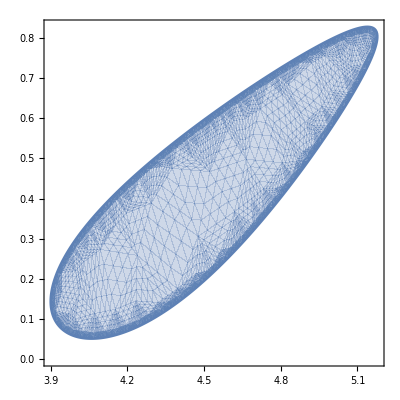

```mathematica
RegionPlot@ImplicitRegion[{H,c}∈ℛfinal,{{H,northpole,southpole},{c,0,1}}]
```

## Period with Integrand: jacobian/Sqrt[snormχHc]

```mathematica
sXrc=Xrc//Subspecifics//Simplify;
sXHc=sXrc//SubHc//Subspecifics;
sTc=D[sXHc,c];
sTH=D[sXHc,H];
snormTc=IP[sTc,sTc];
(*snormTcrc=IP[sTrc,sTrc];*)
snormTH=IP[sTH,sTH];
sTHc=IP[sTH,sTc];
```

```mathematica
sVVHc=((VV//Subrc)//Subspecifics)//SubHc;

(* For Mathematical Derivation of this formula, see Section5 of "flowchart.tex"
There χ is denoted Subscript[X, H] *)
 (* Let χ be the Hamiltonian vector field associated to the circle action *)
 (* So VV = T χ for some T.  We wish to find T. *)
 (* Using the general formula for Hamiltonian vector fields we have
  Ω(χ, V) = dH (V) where H is the Hamiltonian *)
 (* Set V = ∂X/∂c, which is dcXrc in this code.
 Observe that V is a tangent vector to the manifold because we are 
  parametrizing the manifold by c and rr and this is the directional derivative w.r.t. c *) 
 (* hVH = dcXrc = omega (χ, dcXrc) = Ω(VV/T,dcXrc) = Ω/T,
noting that VH=dcXrc.
Therefore T = Ω/hVH and so χ = Ω/hVH VV
 *)  
χ=hVH/Ω̂ VV;
sχ = χ//Subspecifics;
sχrc=(sχ//Subrc)//Subspecifics;
snormχrc=IP[sχrc,sχrc]//Subspecifics;
snormχHc=(snormχrc//SubHc)//Subspecifics;
```

```mathematica
jacobian=Sqrt[Det[{{snormTc,sTHc},{sTHc,snormTH}}]];

integrand=(jacobian/Sqrt[snormχHc]);
```

```mathematica
(*Calculate period along H=z with above integrand*)
Periodχ[z_]:=NIntegrate[integrand/.H->z,{H,c}∈ImplicitRegion[{H,c}∈ℛfinal&&H==z,{H,c}]]
```

```mathematica
(*Table of Half-Periods with Above Integrand with z=H from SP to NP in main region*)
(* This generates the Table 1 §4.1 *)
Table[{z,Periodχ[z]},{z,southpole-0.1,northpole,-0.1}]
```

{{5.07858,5.83862},{4.97858,5.07163},{4.87858,4.64813},{4.77858,4.57605},{4.67858,4.8062},{4.57858,4.97467},{4.47858,3.57818},{4.37858,2.78557},{4.27858,2.28502},{4.17858,1.94104},{4.07858,1.69484},{3.97858,1.52715}}